#### Importing data from Julia

```mathematica
SetDirectory[NotebookDirectory[]];
datawigner=Import["wignertest_kicked.dat"];
datahusimi=Import["husimitest_kicked.dat"];
dataresonances=Import["resonances_kicked.dat"];
```

```mathematica
qf[theta_,phi_]=Cos[phi]*(2*(1-Cos[theta]))^(1/2);
pf[theta_,phi_]=-Sin[phi]*(2*(1-Cos[theta]))^(1/2);
```

```mathematica
NN=100;(*Number of subintervals in the grid (must coincide the N in the Julia code)*)
J=50;(* Total angular momentum (must coincide the J in the Julia code)*)
Hvol=((2*J+1)/4)*Sum[(π/NN)*(2*π/NN)*Sin[datahusimi[[i,1]]]*datahusimi[[i,3]],{i,1,Length[datahusimi]}](*Volume of the Husimi function*)
Wvol=Sum[(π/NN)*(2*π/NN)*Sin[datawigner[[i,1]]]*datawigner[[i,3]],{i,1,Length[datawigner]}](*Volume of the Wigner function*)
Wneg=Sum[(π/NN)*(2*π/NN)*Sin[datawigner[[i,1]]]*Abs[datawigner[[i,3]]],{i,1,Length[datawigner]}]-1(*Wigner negativity*)
datahusimipq=Table[{qf[datahusimi[[i,1]],datahusimi[[i,2]]],pf[datahusimi[[i,1]],datahusimi[[i,2]]],datahusimi[[i,3]]},{i,1,Length[datahusimi]}];
datawignerpq=Table[{qf[datawigner[[i,1]],datawigner[[i,2]]],pf[datawigner[[i,1]],datawigner[[i,2]]],datawigner[[i,3]]},{i,1,Length[datawigner]}];
```

0.996123

0.992246

0.0595061

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

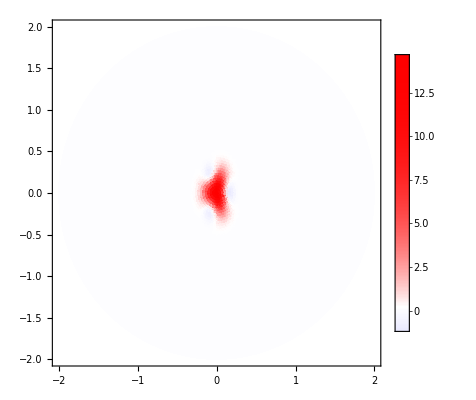

```mathematica
(*Wigner function and Poncaire sections*)wigner2=Show[ListDensityPlot[datawignerpq,PlotRange->{{-2,2},{-2,2},All},Frame->  True,LabelStyle->Directive[Bold,Medium],ColorFunction->(FCo[1-0.5/15.75(#+15.6)]&),ColorFunctionScaling->False,PlotLegends->Automatic],ListPlot[{},PlotStyle->Darker[Green]]]
```

```mathematica
Export["resonance3_RegionI.png",wigner2]
```

resonance3_RegionI.png

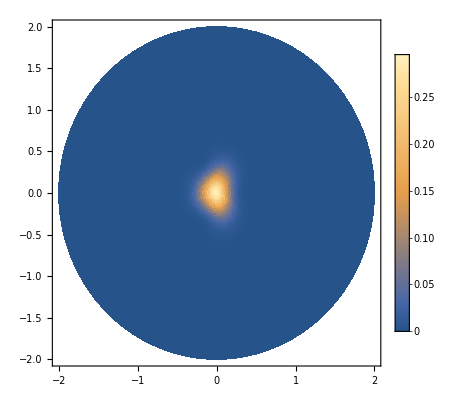

```mathematica
ListDensityPlot[datahusimipq,PlotRange->{{-2,2},{-2,2},All},Frame->True,PlotLegends->Automatic]
```

```mathematica
Tres=14;(*T(E_0)*)
DataExpH0=Table[{dataresonances[[i,1]],dataresonances[[i,2]]},{i,1,Length[dataresonances]}];
DataQFIJz=Table[{dataresonances[[i,1]],dataresonances[[i,3]]},{i,1,Length[dataresonances]}];
```

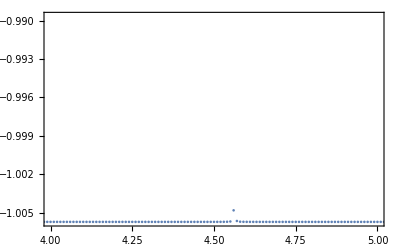

```mathematica
ListPlot[DataExpH0,PlotRange->{{4,5},All},Joined->False,Frame->True,LabelStyle->{Black,15},GridLines->{{},{}},GridLinesStyle->{{Dashed,Red},{}}]
```

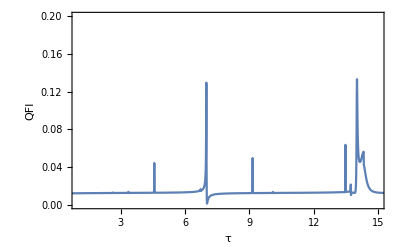

```mathematica
qfi=ListPlot[DataQFIJz,Joined->True,Frame->True,PlotRange->{{1,15},{0,0.2}},FrameLabel->{"τ","QFI"},LabelStyle->{Black,15}]
```

```mathematica
Export["qfi_kickedLMG.png",qfi]
```

qfi_kickedLMG.png